## Cross Section Dimensionality

I’m going to do things in SI units here, even though for nuclear physics that’s not the best set of units (natural units are). But the concepts are the same. First step is to get the reduced mass of an α ^235U system.

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[m, α]]
```

```mathematica
Symbolize[Subscript[m, U]]
```

```mathematica
Subscript[m, α] = Quantity[6.64*^-27,"Kilograms"]
```

6.64×10^-27 kg

```mathematica
u = Quantity[1.66*^-27,"Kilograms"]
```

1.66×10^-27 kg

```mathematica
Subscript[m, U] = 235.04*u
```

3.90166×10^-25 kg

```mathematica
μ = Subscript[m, α]*Subscript[m, U]/(Subscript[m, α] + Subscript[m, U])
```

6.52889×10^-27 kg

got the reduced mass μ, now we can try to construct the denominator of the integral on pg 364 or 365, given a specific impact parameter, and initial kinetic energy T_0. Actually, the form on pg 365 is better because the denominator was divided by a factor of the initial kinetic energy.

```mathematica
Symbolize[Subscript[R, U]]
```

```mathematica
Subscript[R, U] = Quantity[7.4*^-15,"Meters"]
```

7.4×10^-15 m

```mathematica
b = 10000*Subscript[R, U]
```

7.4×10^-11 m

```mathematica
Symbolize[Subscript[T, 0]]
```

```mathematica
Subscript[T, 0] = UnitConvert[Quantity[1*^6,"eV"],"Joules"]
```

801088317/5000000000000000000000 J

```mathematica
k = Quantity[8.98755*^9,"Newtons"*"Meters"^2/"Coulombs"^2]
```

8.98755×10^9 m^2 N/C^2

```mathematica
Symbolize[Subscript[q, α]]
```

```mathematica
Symbolize[Subscript[q, U]]
```

```mathematica
Subscript[q, α] = UnitConvert[Quantity[2,"ElectronCharge"],"Coulombs"]
```

801088317/2500000000000000000000000000 C

```mathematica
Subscript[q, U] = UnitConvert[Quantity[2,"ElectronCharge"],"Coulombs"]
```

801088317/2500000000000000000000000000 C

```mathematica
U[r_]:=  Subscript[q, α]*Subscript[q, U]*k/Quantity[r,"Meters"]
```

```mathematica
U[QuantityMagnitude@b]
```

1.24707×10^-17 m N

```mathematica
d[r_] = 1- (b^2/Quantity[r,"Meters"]^2) - (U[r]/Subscript[T, 0])
```

1-(5.476×10^-21)/r^2-(5.75986×10^-15)/r

```mathematica
d[1*QuantityMagnitude@b]
```

-0.0000778359

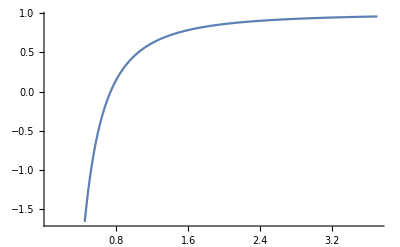

```mathematica
Plot[d[x],{x,0.1*QuantityMagnitude@b,5*QuantityMagnitude@b}]
```